```mathematica
ClearAll[algnormZ2,FindTupleZ2,pCond1Z2,pCond2Z2];
```

```mathematica
AppendTo[$Path,"/homes/tjakobi/PhD_Work/radialprojection/mathematica/packages"];
```

```mathematica
<<EuclideanAlgorithmZSqrt2`
```

```mathematica
(* Computes the algebraic norm of x = m + n * Sqrt[2] in Z[Sqrt[2]]. *)
algnormZ2[{m_Integer,n_Integer}]:=m^2-2*n^2;
```

```mathematica
(* Assuming that p = +1 or -1 (mod 8), this finds the tuple *)
(* (m,n) that solves the equation algnorm(m,n) = p. *)
FindTupleZ2[p_Integer]:=Block[{x,y},
x=Ceiling[Sqrt[p]];
While[True,y=Sqrt[(x^2-p)/2];
If[Element[y,Integers],Return[{x,y}]];
x=x+1;]];
```

```mathematica
(* The two conditions that apply to our visibility checks: *)
(* p = +1 or -1 (mod 8) (first condition) *)
(* p = +3 or -3 (mod 8) (second condition) *)
pCond1Z2[p_Integer]:=Mod[p-1,8]==0||Mod[p+1,8]==0;
pCond2Z2[p_Integer]:=Mod[p-3,8]==0||Mod[p+3,8]==0;
```

```mathematica
(* Check application of first condition to some primes. *)
Select[Table[Prime[i],{i,1,50}],pCond1Z2]
```

{7,17,23,31,41,47,71,73,79,89,97,103,113,127,137,151,167,191,193,199,223}

```mathematica
(* Check tuple computation for some primes. *)
Map[FindTupleZ2,%]
```

{{3,1},{5,2},{5,1},{7,3},{7,2},{7,1},{11,5},{9,2},{9,1},{11,4},{13,6},{11,3},{11,2},{15,7},{13,4},{13,3},{13,1},{17,7},{15,4},{19,9},{15,1}}

```mathematica
ClearAll[ConjZ2,MultZ2,SquareZ2,CubeZ2];
ClearAll[IsDivComp,divTest2Free1Z2,divTest2Free2Z2];
ClearAll[visibility2FreeZ2];
```

```mathematica
(* Conjugate operation: a1 + b1 * Sqrt[2] --> a1 - b1 * Sqrt[2]. *)
ConjZ2[{a1_Integer, b1_Integer}]:={a1,-b1};
```

```mathematica
(* Multiplication, squaring and cubing of elements of Z[Sqrt[2]] *)
MultZ2[{a1_Integer, b1_Integer}, {a2_Integer, b2_Integer}]:={a1*a2+2*b1*b2,a1*b2+a2*b1};
SquareZ2[{a_Integer,b_Integer}]:={a^2+2*b^2,2*a*b};
CubeZ2[{a_Integer,b_Integer}]:={a^3+6*a*b^2,3*a^2*b+2*b^3};
```

```mathematica
(* Check if c divides both components of x = a + b * Sqrt[2] *)
IsDivComp[{a_Integer,b_Integer},c_Integer]:=Mod[a,c]==0&&Mod[b,c]==0;
```

```mathematica
(* Division test (square-free case) for the primes which satisfy the first condition. *)
divTest2Free1Z2[{m_Integer,n_Integer},p_Integer]:=Block[{t,a1,a2,b1,b2},
t=FindTupleZ2[p]; (* algnorm(t) = p *)
a1 = SquareZ2[t]; (* a1 = t^2 *)
a2 = SquareZ2[ConjZ2[t]]; (* a2 = conj(t)^2 *)
b1=MultZ2[{m,n},a1]; (* b1 = x * a1 *)
b2=MultZ2[{m,n},a2]; (* b2 = x * a2 *)
Return[IsDivComp[b1,p^2]||IsDivComp[b2,p^2]];
];
```

```mathematica
(* Division test (square-free case) for the primes which satisfy the second condition. *)
divTest2Free2Z2[{m_Integer,n_Integer},p_Integer]:=IsDivComp[{m,n},p^2];
```

```mathematica
(* Check for square-free 'visibility' of an element of Z[Sqrt[2]]. *)
visibility2FreeZ2[{m_Integer,n_Integer}]:=Block[{norm,primes,c},
If[Mod[m-n,2]==0&&Mod[m,2]==0,Return[False]];
norm=algnormZ2[{m,n}];
If[Abs[norm]==1,Return[True]];
primes=Map[Part[#,1]&,FactorInteger[Abs[norm]]];
c=Catch[Flatten[Map[Function[t,
If[pCond1Z2[t],If[divTest2Free1Z2[{m,n},t],Throw[False]],
If[pCond2Z2[t],If[divTest2Free2Z2[{m,n},t],Throw[False]]]]
],primes],1]];
If[c===False,Return[False],Return[True]];
];
```

```mathematica
ClearAll[vTableZ2,miEmbedZ2,vDrawZ2,checkBoxZ2,cutBoxZ2];
```

```mathematica
(* Generate a list of elements (which later become vertices) of Z[Sqrt[2]]. *)
vTableZ2[r_Integer]:=Flatten[Table[{i,j},{i,-r,r},{j,-Ceiling[r/Sqrt[2]],Ceiling[r/Sqrt[2]]}],1];
```

```mathematica
(* miEmbedZ2 takes an element of Z[Sqrt[2]] in the form {a, b}, where *)
(* x = a + b * Sqrt[2] and then maps it to the Minkowski embedding. *)
miEmbedZ2[{a_Integer,b_Integer}]:=a*{1,1}+b*{Sqrt[2],-Sqrt[2]};
```

```mathematica
(* Map elements to Minkowski embedding and draw the resulting set. *)
vDrawZ2[in_,axes_:True,pstyle_:Automatic]:=ListPlot[Map[miEmbedZ2,in],Axes->axes,PlotStyle->pstyle];
```

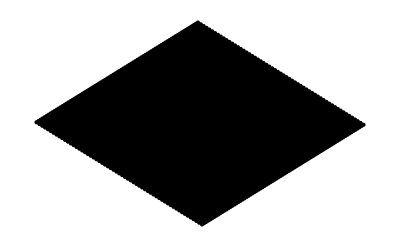

```mathematica
vDrawZ2[vTableZ2[40],False,{PointSize[Tiny],Black}]
```

```mathematica
checkBoxZ2[in_,xmax_,ymax_]:=Block[{mi},
mi=miEmbedZ2[in];
Return[Abs[Part[mi,1]]≤xmax&&Abs[Part[mi,2]]≤ymax]];
```

```mathematica
cutBoxZ2[in_,xmax_,ymax_]:=Select[in,checkBoxZ2[#,xmax,ymax]&];
```

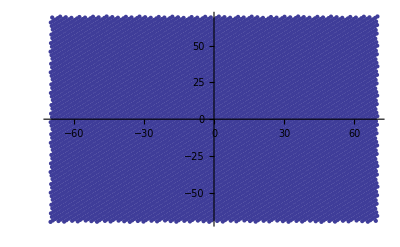

```mathematica
vDrawZ2[cutBoxZ2[vTableZ2[80],70,70]]
```

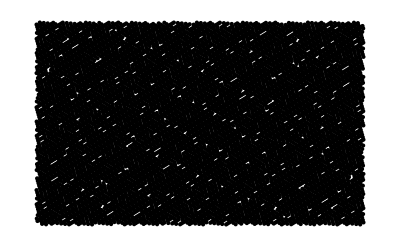

```mathematica
vDrawZ2[cutBoxZ2[Select[vTableZ2[120],visibility2FreeZ2],100,100],False,{PointSize[Tiny],Black}]
```

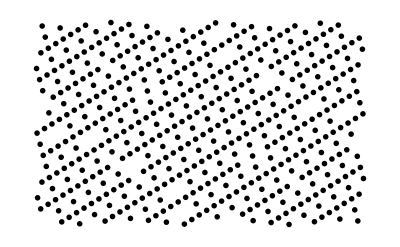

```mathematica
vDrawZ2[cutBoxZ2[Select[vTableZ2[20],visibility2FreeZ2],22,22],False,{PointSize[0.01],Black}]
```

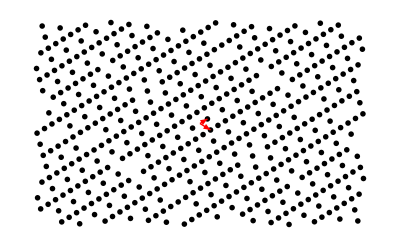

```mathematica
Show[%,
Graphics[{Red,Arrowheads[0.011],Arrow[{{0,0},{1,1}}],Arrow[{{0,0},{Sqrt[2],-Sqrt[2]}}]}]]
```

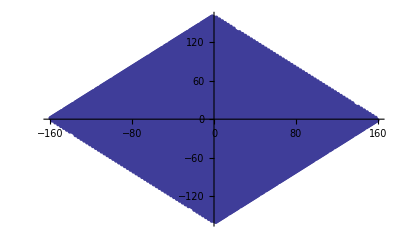

```mathematica
vDrawZ2[Select[vTableZ2[80],visibility2FreeZ2]]
```

```mathematica
(* Compute numerical density: *)
Function[x,N[Length[Select[vTableZ2[x],visibility2FreeZ2]]/Length[vTableZ2[x]]]][180]
```

0.695086

```mathematica
Function[x,N[Length[Select[vTableZ2[x],visibility2FreeZ2]]/Length[vTableZ2[x]]]][150]
```

0.697705

```mathematica
N[Sqrt[2]/(DirichletL[8,1,2]*Zeta[2])]
```

0.696878

```mathematica
(* Compute exact density. Seems to match the numerics quite well. *)
N[1/(DirichletL[8,2,2]*Zeta[2])]
```

0.696878

```mathematica
FullSimplify[1/(DirichletL[8,2,2]*Zeta[2])]
```

(48 √2)/π^4

```mathematica
ClearAll[DivZ2,IsDivZ2,denomZ2,pTest1Z2,factorZ2];
```

```mathematica
(* Let x1 = a1 + b1 * Sqrt[2], x2 = a2 + b2 * Sqrt[2], then this *)
(* computes x1/x2 in Z[Sqrt[2]], assuming that x2 divides x1. *)
DivZ2[{a1_Integer, b1_Integer}, {a2_Integer, b2_Integer}]:=Block[{n,x,y},
n=algnormZ2[{a2,b2}];
x=a1*a2-2*b1*b2;
y=a2*b1-a1*b2;
{Divide[x,n],Divide[y,n]}
];
```

```mathematica
(* Check if x2 divides x1 (x1 and x2 defined like in DivZ2). *)
IsDivZ2[{a1_Integer, b1_Integer}, {a2_Integer, b2_Integer}]:=Block[{n,x,y},
n=algnormZ2[{a2,b2}];
x=a1*a2-2*b1*b2;
y=a2*b1-a1*b2;
Mod[x,n]==0&&Mod[y,n]==0
];
```

```mathematica
(* Let x = (a + b * Sqrt[2]) / c, then this computes the denominator *)
(* in the Fourier module Z[Sqrt[2]] * (Sqrt[2]/4) *)
denomZ2[{{a_Integer,b_Integer},c_Integer}]:=Block[{x,g},
x={4*b,2*a};
g=GCDZ2[{c,0},x];
Return[DivZ2[{c,0},g]];
];
```

```mathematica
pTest1Z2[{m_Integer,n_Integer},p_Integer]:=Block[{t},
t=FindTupleZ2[p];
Select[{t,ConjZ2[t]},IsDivZ2[{m,n},#]&]
];
```

```mathematica
(* Generate a list of primes (in Z[Sqrt[2]]) that divide m + n * Sqrt[2]. *)
factorZ2[{m_Integer,n_Integer}]:=Block[{norm,nprimes},
norm=algnormZ2[{m,n}];
If[Abs[norm]==1,Return[{}]];
nprimes=Map[Part[#,1]&,FactorInteger[Abs[norm]]];
Flatten[Map[Function[x,
If[Mod[x,2]==0,{{0,1}}, (* if we encounter the prime '2', we have a factor of Sqrt[2] *)
If[pCond2Z2[x],{{x,0}},
If[pCond1Z2[x],pTest1Z2[{m,n},x]]]]
],nprimes],1]
];
```

```mathematica
factorZ2[{13,7}]
```

{{11,-5}}

```mathematica
ClearAll[zetaZ2,intensityZ2,qCoprime,qCoprimeCheck];
ClearAll[vTableQ2,vTableQ2Recip,ReduceQ2];
```

```mathematica
zetaZ2=1/(DirichletL[8,2,2]*Zeta[2]);
FullSimplify[zetaZ2]
```

```mathematica
(* Compute the intensity of an element x = m + n * Sqrt[2] of Z[Sqrt[2]]. *)
(* Input of this function are going to be the denominators of elements of Q[Sqrt[2]]. *)
intensityZ2[{m_Integer,n_Integer}]:=Block[{f,prod},
If[m==0&&n==0,Return[0]];
f=1/(2*Sqrt[2]*zetaZ2);
prod=Apply[Times,Map[1/(algnormZ2[#]^2-1)&,factorZ2[{m,n}]]];
Return[(f*prod)^2];
];
```

```mathematica
(* Given an element (a + b * Sqrt[2]) / c, qCoprime checks that this representations can *)
(* not be reduced any further (the integers {a,b,c} are coprime). qCoprimeCheck is just *)
(* a consistency check to verify that this approach is working correctly. *)
qCoprime[{{a_Integer,b_Integer},c_Integer}]:=Abs[GCD[a,b,c]]==1;
qCoprimeCheck[{{a_Integer,b_Integer},c_Integer}]:=(Abs[c]==1)||(Mod[a,c]≠0||Mod[b,c]≠0);
```

```mathematica
(* Generate a list of elements of Q[Sqrt[2]] in the form (a + b * Sqrt[2]) / 2. An element *)
(* is encoded as {{a,b},c}. vTable (see above) is used to generate the {a,b} part of the list. *)
(* Then another pass 'extends' each {a,b} with a 'c' in the range {1,...,s}. *)
vTableQ2[r_,s_]:=Flatten[Map[Function[x,Table[{x,i},{i,1,s}]],vTableZ2[r]],1];
```

```mathematica
(* Same as vTableQ2, but create elements with respect to the basis of the reciprocal lattice. *)
vTableQ2Recip[r_,s_]:=Flatten[Map[Function[x,Table[{{2*Part[x,1],Part[x,2]},4*i},{i,1,s}]],vTableZ2[r]],1];
ReduceQ2[{{a_Integer,b_Integer},c_Integer}]:={{a,b},c}/GCD[a,b,c];
```

```mathematica
(* Alternate version of vTableQ2Recip, still needs some tuning. *)
vTableQ2RecipAlt[r_,s_]:=Union[Flatten[ParallelTable[{{2*a,b},4*c}/GCD[2*a,b,4*c],{c,1,s},{a,-r,r},{b,-r,r}],2]];
```

```mathematica
ClearAll[testCoprime1,testCoprime2];
ClearAll[divTest3Free1Z2,divTest3Free2Z2,visiblity3FreeZ2];
```

```mathematica
testCoprime1=Select[vTableQ2[4,2],qCoprime]
```

{{{-4,-3},1},{{-4,-3},2},{{-4,-2},1},{{-4,-1},1},{{-4,-1},2},{{-4,0},1},{{-4,1},1},{{-4,1},2},{{-4,2},1},{{-4,3},1},{{-4,3},2},{{-3,-3},1},{{-3,-3},2},{{-3,-2},1},{{-3,-2},2},{{-3,-1},1},{{-3,-1},2},{{-3,0},1},{{-3,0},2},{{-3,1},1},{{-3,1},2},{{-3,2},1},{{-3,2},2},{{-3,3},1},{{-3,3},2},{{-2,-3},1},{{-2,-3},2},{{-2,-2},1},{{-2,-1},1},{{-2,-1},2},{{-2,0},1},{{-2,1},1},{{-2,1},2},{{-2,2},1},{{-2,3},1},{{-2,3},2},{{-1,-3},1},{{-1,-3},2},{{-1,-2},1},{{-1,-2},2},{{-1,-1},1},{{-1,-1},2},{{-1,0},1},{{-1,0},2},{{-1,1},1},{{-1,1},2},{{-1,2},1},{{-1,2},2},{{-1,3},1},{{-1,3},2},{{0,-3},1},{{0,-3},2},{{0,-2},1},{{0,-1},1},{{0,-1},2},{{0,0},1},{{0,1},1},{{0,1},2},{{0,2},1},{{0,3},1},{{0,3},2},{{1,-3},1},{{1,-3},2},{{1,-2},1},{{1,-2},2},{{1,-1},1},{{1,-1},2},{{1,0},1},{{1,0},2},{{1,1},1},{{1,1},2},{{1,2},1},{{1,2},2},{{1,3},1},{{1,3},2},{{2,-3},1},{{2,-3},2},{{2,-2},1},{{2,-1},1},{{2,-1},2},{{2,0},1},{{2,1},1},{{2,1},2},{{2,2},1},{{2,3},1},{{2,3},2},{{3,-3},1},{{3,-3},2},{{3,-2},1},{{3,-2},2},{{3,-1},1},{{3,-1},2},{{3,0},1},{{3,0},2},{{3,1},1},{{3,1},2},{{3,2},1},{{3,2},2},{{3,3},1},{{3,3},2},{{4,-3},1},{{4,-3},2},{{4,-2},1},{{4,-1},1},{{4,-1},2},{{4,0},1},{{4,1},1},{{4,1},2},{{4,2},1},{{4,3},1},{{4,3},2}}

```mathematica
testCoprime2=Select[vTableQ2[4,2],qCoprimeCheck]
```

{{{-4,-3},1},{{-4,-3},2},{{-4,-2},1},{{-4,-1},1},{{-4,-1},2},{{-4,0},1},{{-4,1},1},{{-4,1},2},{{-4,2},1},{{-4,3},1},{{-4,3},2},{{-3,-3},1},{{-3,-3},2},{{-3,-2},1},{{-3,-2},2},{{-3,-1},1},{{-3,-1},2},{{-3,0},1},{{-3,0},2},{{-3,1},1},{{-3,1},2},{{-3,2},1},{{-3,2},2},{{-3,3},1},{{-3,3},2},{{-2,-3},1},{{-2,-3},2},{{-2,-2},1},{{-2,-1},1},{{-2,-1},2},{{-2,0},1},{{-2,1},1},{{-2,1},2},{{-2,2},1},{{-2,3},1},{{-2,3},2},{{-1,-3},1},{{-1,-3},2},{{-1,-2},1},{{-1,-2},2},{{-1,-1},1},{{-1,-1},2},{{-1,0},1},{{-1,0},2},{{-1,1},1},{{-1,1},2},{{-1,2},1},{{-1,2},2},{{-1,3},1},{{-1,3},2},{{0,-3},1},{{0,-3},2},{{0,-2},1},{{0,-1},1},{{0,-1},2},{{0,0},1},{{0,1},1},{{0,1},2},{{0,2},1},{{0,3},1},{{0,3},2},{{1,-3},1},{{1,-3},2},{{1,-2},1},{{1,-2},2},{{1,-1},1},{{1,-1},2},{{1,0},1},{{1,0},2},{{1,1},1},{{1,1},2},{{1,2},1},{{1,2},2},{{1,3},1},{{1,3},2},{{2,-3},1},{{2,-3},2},{{2,-2},1},{{2,-1},1},{{2,-1},2},{{2,0},1},{{2,1},1},{{2,1},2},{{2,2},1},{{2,3},1},{{2,3},2},{{3,-3},1},{{3,-3},2},{{3,-2},1},{{3,-2},2},{{3,-1},1},{{3,-1},2},{{3,0},1},{{3,0},2},{{3,1},1},{{3,1},2},{{3,2},1},{{3,2},2},{{3,3},1},{{3,3},2},{{4,-3},1},{{4,-3},2},{{4,-2},1},{{4,-1},1},{{4,-1},2},{{4,0},1},{{4,1},1},{{4,1},2},{{4,2},1},{{4,3},1},{{4,3},2}}

```mathematica
Sort[testCoprime1]==Sort[testCoprime2]
```

True

```mathematica
(* Division test (cube-free case) for the primes which satisfy the first condition. *)
divTest3Free1Z2[{m_Integer,n_Integer},p_Integer]:=Block[{t,a1,a2,b1,b2},
t=FindTupleZ2[p]; (* algnorm(t) = p *)
a1=CubeZ2[t]; (* a1 = t^3 *)
a2=CubeZ2[ConjZ2[t]]; (* a2 = conj(t)^3 *)
b1=MultZ2[{m,n},a1]; (* b1 = x * a1 *)
b2=MultZ2[{m,n},a2]; (* b2 = x * a2 *)
Return[IsDivComp[b1,p^3]||IsDivComp[b2,p^3]];
];
```

```mathematica
(* Division test (cube-free case) for the primes which satisfy the second condition. *)
divTest3Free2Z2[{m_Integer,n_Integer},p_Integer]:=IsDivComp[{m,n},p^3];
```

```mathematica
(* Check for cube-free 'visibility' of an element of Z[Sqrt[2]]. *)
visiblity3FreeZ2[{m_Integer,n_Integer}]:=Block[{norm,primes,c},
If[IsDivZ2[{m,n},{0,2}],Return[False]]; (* check if divisible by (Sqrt[2])^3 = 2*Sqrt[2] *)
norm=algnormZ2[{m,n}];
If[Abs[norm]==1,Return[True]];
primes=Map[Part[#,1]&,FactorInteger[Abs[norm]]];
(* This catch/throw construction is a bit awkward... *)
c=Catch[Flatten[Map[Function[t,
If[pCond1Z2[t],If[divTest3Free1Z2[{m,n},t],Throw[False]],
If[pCond2Z2[t],If[divTest3Free2Z2[{m,n},t],Throw[False]]]]
],primes],1]];
If[c===False,Return[False],Return[True]];
];
```

```mathematica
ClearAll[miEmbedQ2,miEmbedQ2Trans,intensityPlotZ2];
ClearAll[AlwaysTrue,testCutZ2];
```

```mathematica
(* miEmbedQ2 takes an element of Q[Sqrt[2]], written in the form *)
(* x = (a + b * Sqrt[2]) / c, and maps x to the Minkowski embedding. *)
miEmbedQ2[{{a_Integer,b_Integer},c_Integer}]:=miEmbedZ2[{a,b}]/c;
```

```mathematica
(* Do the same as miEmbedQ2, but first map the element x to M^star, where *)
(* M = Q[Sqrt[2]]. In this case this corresponds to multiplication with Sqrt[2]/4. *)
miEmbedQ2Trans[{{a_Integer,b_Integer},c_Integer}]:=miEmbedQ2[{{2*b,a},4*c}];
```

```mathematica
intensityPlotZ2[in_,scaleFunc_,cutFunc_]:=Block[{temp},
temp=Map[{#,denomZ2[#]}&,Select[in,cutFunc]];
Graphics[
Map[Circle[N[miEmbedQ2[Part[#,1]]],scaleFunc[N[intensityZ2[Part[#,2]]]]]&,
Select[temp,visiblity3FreeZ2[Part[#,2]]&]]
]
];
```

```mathematica
toSage[{{x_,y_},r_}]:=StringJoin["circle((",ToString[x],",",ToString[y],
"),",ToString[r],",color='black',thickness=0.5)"];
```

```mathematica
intensityExportZ2[in_,scaleFunc_,cutFunc_,fname_]:=Block[{temp,out},
temp=Map[{#,denomZ2[#]}&,Select[in,cutFunc]];
out=OpenWrite[fname];
WriteString[out,Map[toSage,Map[{N[miEmbedQ2[Part[#,1]]],CForm[scaleFunc[N[intensityZ2[Part[#,2]]]]]}&,
Select[temp,visiblity3FreeZ2[Part[#,2]]&]]]];
Close[out];
];
```

```mathematica
AlwaysTrue[x_]:=True;
```

```mathematica
testCutZ2[x_]:=Norm[N[miEmbedQ2[x]]]≤1.2;
```

```mathematica
(* Point against line clipping test. Line is defined *)
(* by (p0,p1) and the point tested is 't'. *)
clipLinePoint[{p0x_,p0y_},{p1x_,p1y_},{tx_,ty_}]:=
(p1x- p0x) * (ty - p0y) - (p1y - p0y) * (tx - p0x);
```

```mathematica
lvec1Z2:={1/2,1/2};
lvec2Z2:={Sqrt[2]/4,-Sqrt[2]/4};
clipEps=0.0001;
```

```mathematica
(* Box clipping test, currently using the basis vectors of the reciprocal lattice. *)
(* Two times two fundamental domains are cut. *)
clipCutZ2[x_]:=Block[{y},
y=N[miEmbedQ2[x]];
If[clipEps+clipLinePoint[lvec2Z2+{0,0},lvec2Z2+lvec1Z2,y]<0,Return[False]];
If[clipEps+clipLinePoint[-lvec2Z2+lvec1Z2,-lvec2Z2+{0,0},y]<0,Return[False]];
If[clipEps+clipLinePoint[-lvec1Z2+{0,0},-lvec1Z2+lvec2Z2,y]<0,Return[False]];
If[clipEps+clipLinePoint[lvec1Z2+lvec2Z2,lvec1Z2+{0,0},y]<0,Return[False]];
Return[True];
];
```

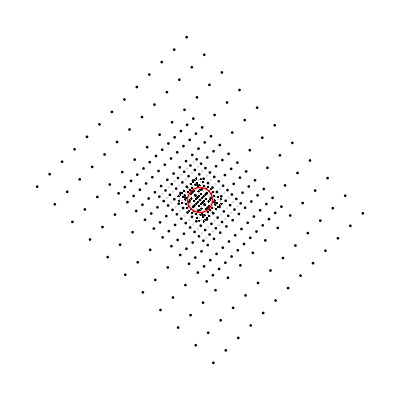

```mathematica
Show[intensityPlotZ2[Select[vTableQ2[6,10],qCoprime],#*0.2&,AlwaysTrue],
Graphics[{Red,Circle[{0,0},1]}]]
```

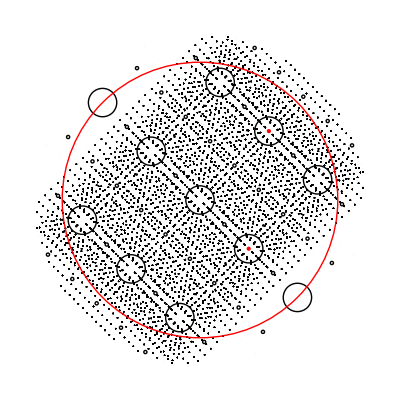

```mathematica
Show[intensityPlotZ2[vTableQ2RecipAlt[18,14],0.4*#&,testCutZ2],
Graphics[{Red,PointSize[Large],Circle[{0,0},1],Point[{{1/2,1/2},{Sqrt[2]/4,-Sqrt[2]/4}}]}]]
```

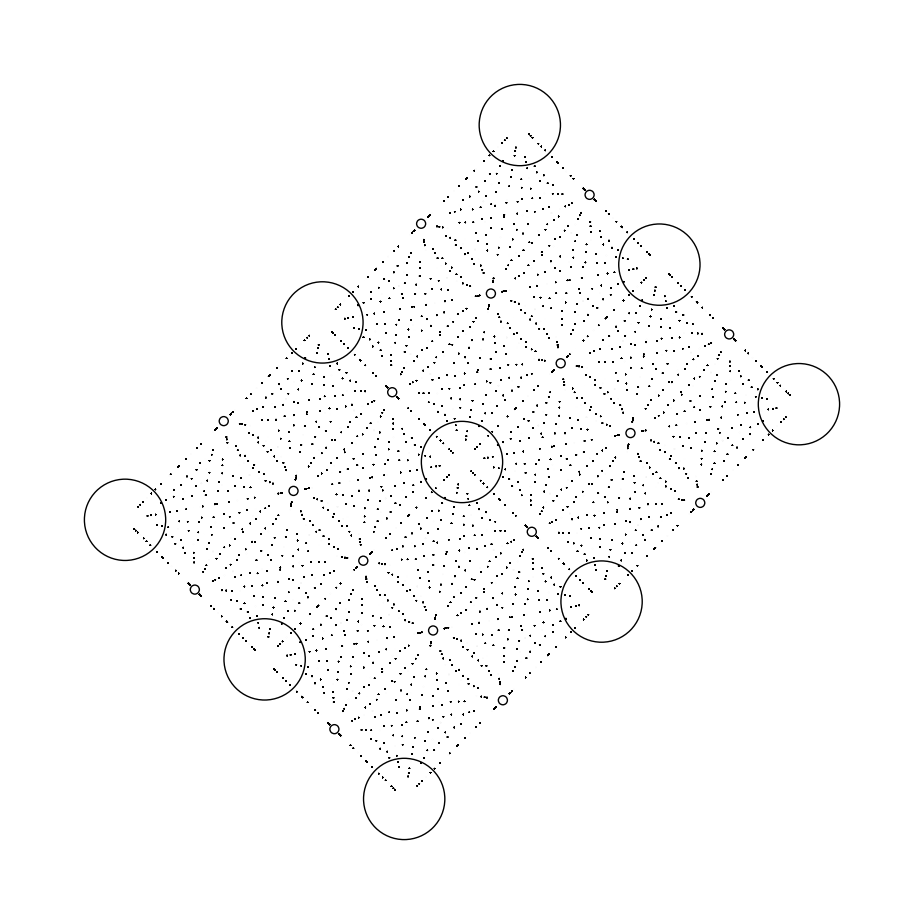

```mathematica
intensityPlotZ2[vTableQ2RecipAlt[20,16],0.4*#&,clipCutZ2]
```

```mathematica
intensityExportZ2[vTableQ2RecipAlt[20,16],#*0.4&,clipCutZ2,"/homes/tjakobi/out_sage.txt"]
```